```mathematica
Animate[MatrixPlot[MM⟦i⟧,FrameTicks->None],{i,1,imax,1}]
```

```mathematica
imax=6;n=3;p=1/9;
MM=Table[IdentityMatrix[3^(i-1)],{i,1,imax}];
For[i=1,i<imax,i=i+1,
MM⟦i+1⟧=Table[MM⟦i,Ceiling[j/n],Ceiling[k/n]⟧*If[Random[]<p,1,0],{j,1,n^i},{k,1,n^i}];]
For[i=1,i<=imax,i=i+1,Pause[0.5];M=MM⟦i⟧];
```

```mathematica
If[2<1,1,3]
```

3

```mathematica
Random[]
```

0.551314

```mathematica
M=Table[IdentityMatrix[n],{n,1,5}];
M⟦3,Ceiling[1/3],Ceiling[1/3]⟧
```

1

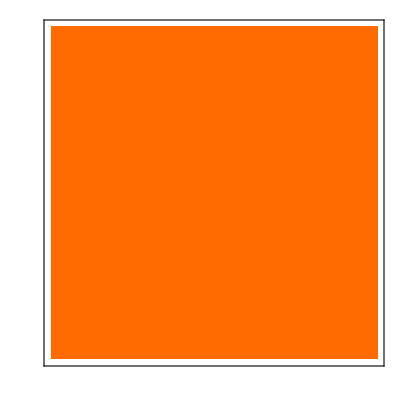
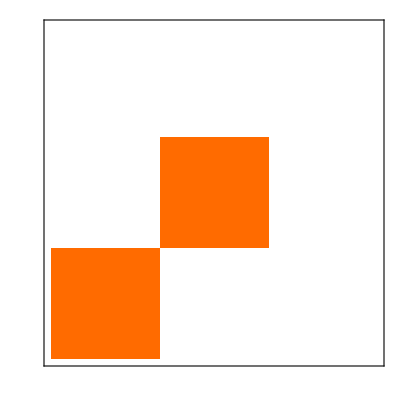
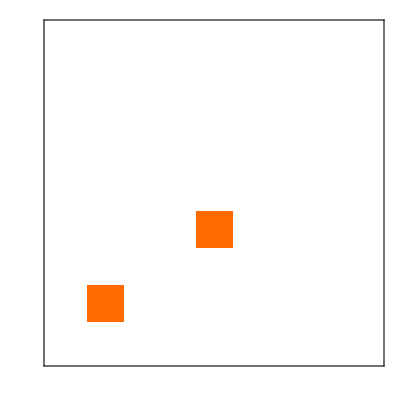
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,FrameTicks->None]&/@MM
```